```mathematica
AVERAGE NUMBER OF NEIGHBOURS
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["graph1.csv","CSV","Numeric"->True];
graph1=Import["graph1.csv","CSV","Numeric"->True];
```

```mathematica
graph1sorted = SortBy[graph1,First]
```

```mathematica
col1=graph1sorted[[All,1]]
col2=graph1sorted[[All,2]];
```

```mathematica
bin=BinCounts[col1,{1,90000}]
```

```mathematica
0.0+Total[bin]/CountDistinct[Union[col1,col2]]
```

50.4663

```mathematica
graph1sorted//Flatten //Union//CountDistinct
```

37377

```mathematica
INFO LEAKAGE
```

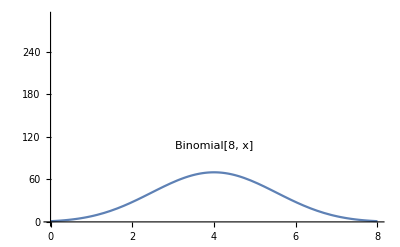

```mathematica
p1 =Plot[Binomial[8,x],{x,0,8}, PlotRange->{{0,8},{0,290}},PlotLabels->Placed[Automatic,Above]]
```

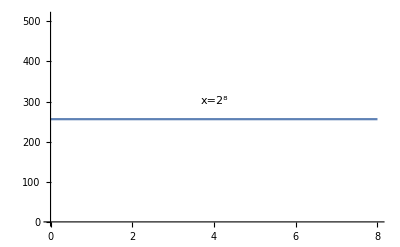

```mathematica
p2 = Plot[x=2^8,{x,0,8},PlotLabels->Placed[Automatic,Above]]
```

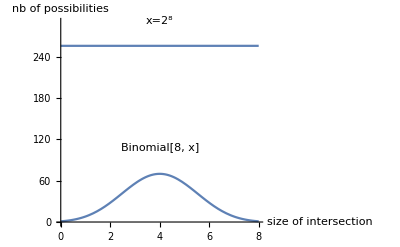

```mathematica
Show[p1,p2, AxesLabel-> {"size of intersection","nb of possibilities"}]
```

## PLOTS WITH DIFFERENT K VALUES

```mathematica
findCardinality[matrix_,index1_, index2_]:= Module[{cardinality},
If[(index1 == index2),cardinality=0];
If[(index1 ≠  index2),cardinality=Total[BitAnd[matrix[[1]][[index1]],matrix[[1]][[index2]]]]];
cardinality
]
findNeighbours[node_,c1_,c2_]:= Module[{neighborlist},
indices=Position[c1, node];
l1=Flatten[Map[c2[[#]]&,indices]];
indices=Position[c2, node];
l2= Flatten[Map[c1[[#]]&,indices]];
neighborlist = Union[l1,l2];
neighborlist
]
removeElements[neighborlist_,node_]:= Module[{newList,alist},
newList= DeleteCases[all,Alternatives@@neighborlist];
alist = {node};
newList = DeleteCases[newList,Alternatives@@alist];
newList
]
```

```mathematica
(*Change parameter k*)
```

```mathematica
gr1 = RandomGraph[BarabasiAlbertGraphDistribution[200,22]];
gr1adj= AdjacencyMatrix[%]//MatrixForm;
gr2= RandomGraph[BarabasiAlbertGraphDistribution[200,44]];
gr2adj =  AdjacencyMatrix[%]//MatrixForm;
gr3 = RandomGraph[BarabasiAlbertGraphDistribution[200,88]];
gr3adj= AdjacencyMatrix[%]//MatrixForm;
gr4= RandomGraph[BarabasiAlbertGraphDistribution[200,176]];
gr4adj =  AdjacencyMatrix[%]//MatrixForm;
Length[gr1adj[[1]][[1]]]
Length[gr2adj[[1]][[1]]]
Length[gr3adj[[1]][[1]]]
Length[gr4adj[[1]][[1]]]
```

200

200

200

«1 more identical outputs»

```mathematica
g1card =Table[findCardinality[gr1adj,i,j],{i,1,Length[gr1adj[[1]][[1]]]},{j,1,Length[gr1adj[[1]][[1]]]}];
```

```mathematica
g2card =Table[findCardinality[gr2adj,i,j],{i,1,Length[gr2adj[[1]][[1]]]},{j,1,Length[gr2adj[[1]][[1]]]}];
```

```mathematica
g3card =Table[findCardinality[gr3adj,i,j],{i,1,Length[gr3adj[[1]][[1]]]},{j,1,Length[gr3adj[[1]][[1]]]}];
```

```mathematica
g4card =Table[findCardinality[gr4adj,i,j],{i,1,Length[gr4adj[[1]][[1]]]},{j,1,Length[gr4adj[[1]][[1]]]}];
```

```mathematica
gr1adj= AdjacencyMatrix[gr1];
gr2adj =  AdjacencyMatrix[gr2];
gr3adj =  AdjacencyMatrix[gr3];
gr4adj =  AdjacencyMatrix[gr4];
Length[gr1adj]
Length[gr2adj]
Length[gr3adj]
Length[gr4adj]
```

200

200

200

«1 more identical outputs»

```mathematica
gr1Ugr2 = MapThread[BitOr[#1,#2]&,{gr1adj,gr2adj}];
gr1Ugr3 = MapThread[BitOr[#1,#2]&,{gr1adj,gr3adj}];
gr1Ugr4 = MapThread[BitOr[#1,#2]&,{gr1adj,gr4adj}];
```

```mathematica
gr1Ugr2=gr1Ugr2//MatrixForm;
gr1Ugr3=gr1Ugr3//MatrixForm;
gr1Ugr4=gr1Ugr4//MatrixForm;
```

```mathematica
g1Ug2card =Table[findCardinality[gr1Ugr2,i,j],{i,1,Length[gr1Ugr2[[1]][[1]]]},{j,1,Length[gr1Ugr2[[1]][[1]]]}];
```

```mathematica
g1Ug3card =Table[findCardinality[gr1Ugr3,i,j],{i,1,Length[gr1Ugr3[[1]][[1]]]},{j,1,Length[gr1Ugr3[[1]][[1]]]}];
```

```mathematica
g1Ug4card =Table[findCardinality[gr1Ugr4,i,j],{i,1,Length[gr1Ugr4[[1]][[1]]]},{j,1,Length[gr1Ugr4[[1]][[1]]]}];
```

```mathematica
Total[Total[g1card]]
Total[Total[g2card]]
Total[Total[g3card]]
Total[Total[g4card]]
Total[Total[g1Ug2card]]
Total[Total[g1Ug3card]]
Total[Total[g1Ug4card]]
```

424294

1372792

3882276

7666516

2038826

4317230

7692336

```mathematica
0.0+Total[Total[g1card]]/(Length[gr1adj]*Length[gr1adj])
0.0+Total[Total[g2card]]/(Length[gr2adj]*Length[gr2adj])
0.0+Total[Total[g3card]]/(Length[gr3adj]*Length[gr3adj])
0.0+Total[Total[g4card]]/(Length[gr4adj]*Length[gr4adj])
0.0+Total[Total[g1Ug2card]]/(Length[g1Ug2card]*Length[g1Ug2card])
0.0+Total[Total[g1Ug3card]]/(Length[g1Ug3card]*Length[g1Ug3card])
0.0+Total[Total[g1Ug4card]]/(Length[g1Ug4card]*Length[g1Ug4card])
```

10.6074

34.3198

97.0569

191.663

50.9707

107.931

192.308

```mathematica
gr2old= RandomGraph[BarabasiAlbertGraphDistribution[200,22]];
gr2adjold =  AdjacencyMatrix[%]//MatrixForm;
Length[gr2adjold[[1]][[1]]]
```

200

```mathematica
g2cardold =Table[findCardinality[gr2adjold,i,j],{i,1,Length[gr2adjold[[1]][[1]]]},{j,1,Length[gr2adjold[[1]][[1]]]}];
```

```mathematica
gr2adjold =  AdjacencyMatrix[gr2old];
Length[gr2adjold]
```

200

```mathematica
gr1Ugr2old = MapThread[BitOr[#1,#2]&,{gr1adj,gr2adjold}];
```

```mathematica
gr1Ugr2old=gr1Ugr2old//MatrixForm;
```

```mathematica
g1Ug2cardold =Table[findCardinality[gr1Ugr2old,i,j],{i,1,Length[gr1Ugr2old[[1]][[1]]]},{j,1,Length[gr1Ugr2old[[1]][[1]]]}];
```

```mathematica
Total[Total[g2cardold]]
Total[Total[g1Ug2cardold]]
0.0+Total[Total[g2cardold]]/(Length[g2cardold]*Length[g2cardold])
0.0+Total[Total[g1Ug2cardold]]/(Length[g2cardold]*Length[g2cardold])
```

431928

1097164

10.7982

27.4291

{22,44,88,176}

{10.6,10.6,10.6,10.6}

{{22,10.6},{44,10.6},{88,10.6},{176,10.6}}

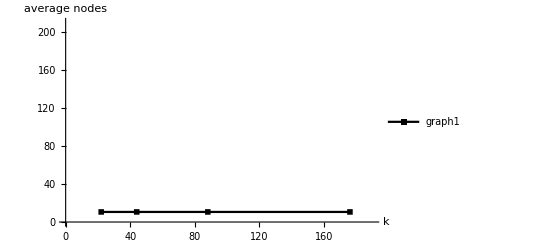

```mathematica
x={22,44,88,176}
y1={10.6,10.6,10.6,10.6}
data=Thread[{x,y1}]
graph1plot=ListPlot[data,Joined->True, PlotMarkers-> {■}, PlotLabel->"", AxesLabel->{"k","average nodes"}, PlotRange->{{0,190},{0,210}}, PlotStyle->{Black},PlotLegends-> {"graph1"}]
```

{{22,10.8},{44,34.3},{88,97.1},{176,191.7}}

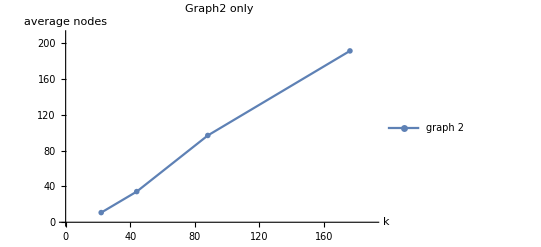

```mathematica
x={22,44,88,176};
y1={10.8,34.3,97.1,191.7};
data=Thread[{x,y1}]
gr2only=ListPlot[data,Joined->True, PlotMarkers->{●}, PlotLabel->"Graph2 only ", AxesLabel->{"k","average nodes"}, PlotRange->{{0,190},{0,210}},PlotLegends-> {"graph 2"}]
```

{22,44,88,176}

{27.4,51,108,192.3}

{{22,27.4},{44,51},{88,108},{176,192.3}}

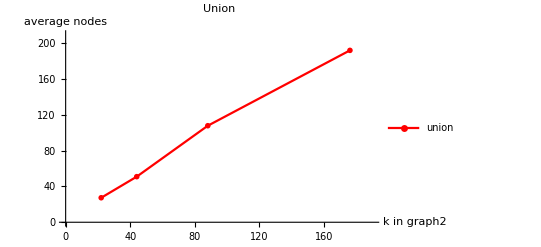

```mathematica
x={22,44,88,176}
y1={27.4,51,108,192.3}
data=Thread[{x,y1}]
union=ListPlot[data,Joined->True, PlotMarkers->{●}, PlotLabel->"Union ", AxesLabel->{"k in graph2","average nodes"}, PlotRange->{{0,190},{0,210}}, PlotStyle->{Red},PlotLegends-> {"union"}]
```

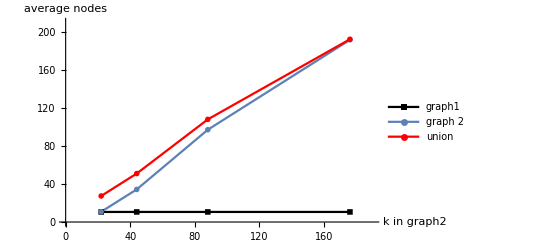

```mathematica
Show[{graph1plot,gr2only,union}, PlotRange->{{0,190},{0,210}}, PlotLabel-> "",AxesLabel->{"k in graph2","average nodes"}]
```